```mathematica
LagrangePolyFactor[j_,k_,xp_]:=If[j!=k,((x-xp[[k]])/(xp[[j]]-xp[[k]])),1]
LagrangePoly[j_,xp_]:=Product[If[j!=k,((x-xp[[k]])/(xp[[j]]-xp[[k]])),1],{k,1,Length[xp]}]
```

### Equal Spacing

{-1,-1/3,1/3,1}

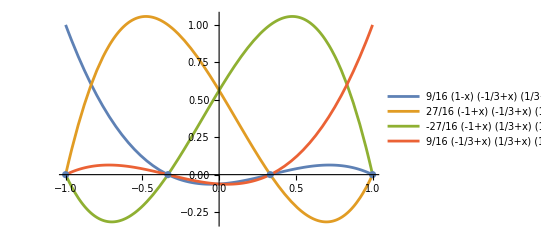

{-0.0083125,0.0511875,0.9725625,-0.0154375}

{0.248125,-1.569375,0.894375,0.426875}

```mathematica
order=3;
xp=Subdivide[-1,1,order]
Points=Table[{xp[[n]],0},{n,1,order+1}];
Bases=Table[LagrangePoly[n,xp],{n,1,order+1}];
Show[Plot[Bases,{x,-1,1},PlotRange->Full,PlotLegends->"Expressions"],ListPlot[Points]]
NumberForm[Bases/.x->0.3,14]
NumberForm[D[Bases,x]/.x->0.3,14]
```

### Gauss-Lobatto Spacing

{-1.,-0.447214,0.447214,1.}

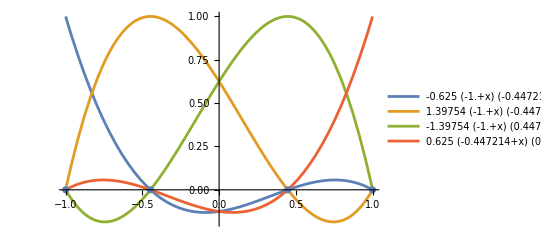

{-0.048125,0.1872209013391,0.9502790986609,-0.089375000000001}

{0.33125,-1.3952060147343,0.64520601473428,0.41875}

```mathematica
GaussLobattoPointsWeights=ResourceFunction["ModifiedGaussianQuadratureWeights"]["Lobatto",order+1];
xp=Table[GaussLobattoPointsWeights[[n,1]],{n,1,order+1}]
Points=Table[{xp[[n]],0},{n,1,order+1}];
Bases=Table[LagrangePoly[n,xp],{n,1,order+1}];
Show[Plot[Bases,{x,-1,1},PlotRange->Full,PlotLegends->"Expressions"],ListPlot[Points]]
NumberForm[Bases/.x->0.3,14]
NumberForm[D[Bases,x]/.x->0.3,14]
```

```mathematica
NumberForm[MatrixForm[GaussLobattoPointsWeights=ResourceFunction["ModifiedGaussianQuadratureWeights"]["Lobatto",9]],14]
```

(-1. | 0.027777777777777
-0.89975799541146 | 0.16549536156081
-0.67718627951074 | 0.27453871250016
-0.36311746382618 | 0.34642851097305
-4.4408920985006×10^-16 | 0.37151927437642
0.36311746382618 | 0.34642851097305
0.67718627951074 | 0.27453871250016
0.89975799541146 | 0.16549536156081
1. | 0.027777777777778)

```mathematica
1/.066666666666665
```

15.

```mathematica
1/"0.37847495629785"
```

2.64218

```mathematica
1/0.55485837703549
```

1.80226

## 3 D product

```mathematica
GLp1=ResourceFunction["ModifiedGaussianQuadratureWeights"]["Lobatto",order+2];
NumberForm[evalPoints={0.31415,-0.161803,0.69314},14]
```

{0.31415,-0.161803,0.69314}

```mathematica
TPBasis3[a_,b_,c_,ξ0_,ξ1_,ξ2_]:=(Bases[[a]]/.x->ξ0)(Bases[[b]]/.x->ξ1)(Bases[[c]]/.x->ξ2)
DTPBasis3[a_,b_,c_,ξ0_,ξ1_,ξ2_]:={ D[TPBasis3[a,b,c,x,ξ1,ξ2],x]/.x->ξ0,
									D[TPBasis3[a,b,c,ξ0,x,ξ2],x]/.x->ξ1,
									D[TPBasis3[a,b,c,ξ0,ξ1,x],x]/.x->ξ2}
```

```mathematica
TPBasis3[2,1,1,ξ0,ξ1,ξ2]
D[TPBasis3[2,1,1,ξ0,ξ1,ξ2],ξ0]
```

0.545915 (-1.+ξ0) (-0.447214+ξ0) (1.+ξ0) (-1.+ξ1) (-0.447214+ξ1) (0.447214+ξ1) (-1.+ξ2) (-0.447214+ξ2) (0.447214+ξ2)

0.545915 (-1.+ξ0) (-0.447214+ξ0) (-1.+ξ1) (-0.447214+ξ1) (0.447214+ξ1) (-1.+ξ2) (-0.447214+ξ2) (0.447214+ξ2)+0.545915 (-1.+ξ0) (1.+ξ0) (-1.+ξ1) (-0.447214+ξ1) (0.447214+ξ1) (-1.+ξ2) (-0.447214+ξ2) (0.447214+ξ2)+0.545915 (-0.447214+ξ0) (1.+ξ0) (-1.+ξ1) (-0.447214+ξ1) (0.447214+ξ1) (-1.+ξ2) (-0.447214+ξ2) (0.447214+ξ2)

```mathematica
Baselines=Table[TPBasis3[a,b,c,evalPoints[[1]],evalPoints[[2]],evalPoints[[3]]],
{a,1,order+1},{b,1,order+1},{c,1,order+1}];
Dimensions[Baselines]
NumberForm[Chop[Baselines,10^-14],14]
```

{4,4,4}

{{{0.00029480662998955,-0.00097875857989107,0.0045384751099593,0.0016266339617432},{-0.0019359683760398,0.0064274187405959,-0.029803754035777,-0.01068195755787},{-0.00090727558355123,0.0030121566864284,-0.013967283076256,-0.0050060111501464},{0.00021269185295386,-0.00070613736183238,0.0032743384392556,0.0011735549889536}},{{-0.0011378239751871,0.0037775777911087,-0.017516518509386,-0.0062780919160148},{0.0074719867512486,-0.024807010418579,0.11502938686857,0.041227659675451},{0.0035016848539094,-0.011625600465498,0.053907571729144,0.019321002064616},{-0.00082089703893853,0.0027253797517944,-0.012637506758901,-0.0045294062846522}},{{-0.0065104039128026,0.021614553541207,-0.10022605704316,-0.03592200117618},{0.042753231468636,-0.14194081089519,0.65817541789208,0.235896520657},{0.020035948680501,-0.066519388244399,0.30844847144075,0.11055095531807},{-0.0046970106192697,0.015594084310833,-0.072309316067706,-0.02591636759405}},{{0.00056487589531351,-0.0018753890614039,0.0086961246128934,0.0031167762933947},{-0.0037094887240253,0.012315509714885,-0.057106660882287,-0.020467586971896},{-0.0017384212409767,0.0057715618713565,-0.026762564780435,-0.0095919655215643},{0.00040753663127406,-0.0013530224014756,0.0062739255813192,0.0022486364201113}}}

```mathematica
Bases
```

{-0.625 (-1.+x) (-0.447214+x) (0.447214+x),1.39754 (-1.+x) (-0.447214+x) (1.+x),-1.39754 (-1.+x) (0.447214+x) (1.+x),0.625 (-0.447214+x) (0.447214+x) (1.+x)}

```mathematica
GradientBaselines=Table[DTPBasis3[a,b,c,evalPoints[[1]],evalPoints[[2]],evalPoints[[3]]],
{a,1,order+1},{b,1,order+1},{c,1,order+1}];
Dimensions[GradientBaselines]
NumberForm[Chop[GradientBaselines,10^-14],14]
```

{4,4,4,3}

{{{{-0.0022581643543929,0.00029510192644433,0.00049656139120705},{0.0074971100098549,-0.0009797389646902,-0.0013683638724197},{-0.034763881385479,0.0045430211258006,-0.008129659246093},{-0.012459715815019,0.0016282632983769,0.0090014617273057}},{{0.014829160314882,0.0025355097937921,-0.0032608735772776},{-0.049232840832939,-0.0084178974033245,0.0089859213275284},{0.22829125312776,0.039033545787594,0.053386734243303},{0.081821822640745,0.013990005384414,-0.059111781993554}},{{0.0069495634560833,-0.0034803363571872,-0.0015281814591224},{-0.023072564071507,0.011554723415225,0.0042111777842445},{0.10698680952879,-0.053578916905431,0.025019251896856},{0.038345121130264,-0.019203208954598,-0.027702248221978}},{{-0.0016291803234792,0.00064972463695073,0.00035825029581226},{0.0054088818146711,-0.0021570870472101,-0.00098722287063344},{-0.025080827890498,0.010002349992036,-0.0058652422063787},{-0.0089892145372337,0.0035849402718072,0.0064942147811999}}},{{{0.0093441519804066,-0.0011389636896706,-0.0019165086486951},{-0.031022602588528,0.0037813616453911,0.005281282923909},{0.1438509072481,-0.017534064131803,0.031376910351826},{0.051557575063891,-0.0062843804390566,-0.03474168462704}},{{-0.0613621977756,-0.0097859530255499,0.012585538311713},{0.20372261490852,0.032489382910104,-0.034681705516492},{-0.94465584884176,-0.15065232500118,-0.20604932182538},{-0.33857391495072,-0.053995269848398,0.22814548903016}},{{-0.028756886984242,0.013432568151752,0.005898108542157},{0.09547292022497,-0.044596152159009,-0.016253294733767},{-0.44270515836947,0.20679106240493,-0.096563312197209},{-0.15866986778498,0.074115943558812,0.10691849838882}},{{0.0067414528603565,-0.0025076514365314,-0.001382688631214},{-0.0223816364925,0.0083254076035137,0.00381024623191},{0.10378299841078,-0.03860467327195,0.022637256166639},{0.037196843824493,-0.013836293271357,-0.025064813767335}}},{{{-0.0040125981661865,-0.0065169251338304,-0.010965883719697},{0.013321833647192,0.021636204007591,0.03021845712715},{-0.06177295573085,-0.10032644962702,0.17953247987466},{-0.022140032780737,-0.035957982862196,-0.19878505328211}},{{0.026350367886122,-0.055993289170731,0.072011962883654},{-0.087483272179944,0.18589782799022,-0.19844186466549},{0.40565739241913,-0.86200282956703,-1.17897349704},{0.14539158535719,-0.30895026274696,1.3054033988218}},{{0.012348882190718,0.076858500226076,0.033747811408771},{-0.040998312679255,-0.25517036891775,-0.092998140255612},{0.19010798522536,1.1832175900427,-0.55251618815512},{0.068136565184096,0.42407678117962,0.61176651700196}},{{-0.0028949380790918,-0.014348285921515,-0.0079114710808963},{0.009611200003422,0.047636336919934,0.021801475903062},{-0.044566855288488,-0.22088831084864,0.12952590588379},{-0.015973197742402,-0.079168535570466,-0.14341591070595}}},{{{-0.0030733894598271,0.00056544170975696,0.00095145607968906},{0.01020365893148,-0.0018772675664469,-0.0026219076808928},{-0.04731407013177,0.0087048351862227,-0.015577154914709},{-0.016957826468134,0.0031198982482497,0.017247606515913}},{{0.020182669574596,0.0048582637537536,-0.0062481257003417},{-0.067006501895641,-0.016129445028182,0.017217829718701},{0.31070720329486,0.074791768166169,0.10229376220141},{0.11136050695279,0.026806102757057,-0.11326346621977}},{{0.0094584413374409,-0.006668636033823,-0.0029281324845166},{-0.031402043474208,0.022139884488033,0.008068993635875},{0.14561036361532,-0.102662001387,0.047939126456591},{0.052188181470621,-0.036795067504097,-0.053079987607949}},{{-0.0022173344577856,0.0012449305703125,0.00068643963875728},{0.007361554674407,-0.0041331718934041,-0.001891607400223},{-0.03413531523179,0.019165398034606,-0.011238329147062},{-0.012234431544858,0.0068690664987904,0.012443496908528}}}}

```mathematica
SeedRandom[1234];
fieldPoints=RandomReal[{-1,1},{order+1,order+1,order+1}];
fieldValue=0;
fieldGradient={0,0,0};
For[a=0,a<order+1,a++,
For[b=0,b<order+1,b++,
For[c=0,c<order+1,c++,
fieldValue += fieldPoints[[a+1,b+1,c+1]]*Baselines[[a+1,b+1,c+1]];
fieldGradient[[1]]+=fieldPoints[[a+1,b+1,c+1]]*GradientBaselines[[a+1,b+1,c+1,1]];
fieldGradient[[2]]+=fieldPoints[[a+1,b+1,c+1]]*GradientBaselines[[a+1,b+1,c+1,2]];
fieldGradient[[3]]+=fieldPoints[[a+1,b+1,c+1]]*GradientBaselines[[a+1,b+1,c+1,3]];
]
]
]
NumberForm[Chop[fieldPoints,10^-14],14]
NumberForm[Chop[fieldValue,10^-14],14]
NumberForm[Chop[fieldGradient,10^-14],14]
```

{{{0.75321698514839,0.043928500403754,-0.82755314609174,-0.24417409139023},{-0.97671085406151,0.85453232668432,0.087513533902136,-0.041336659055151},{-0.50930154443859,0.51979200312318,0.96998599508861,-0.56590975687332},{-0.081965626149824,0.76945833740991,0.1677085719803,-0.47205366499994}},{{0.83912032472826,-0.15232955420577,0.97458062333262,0.17588531238907},{-0.83439021321014,0.58042926096295,0.39231786572069,0.50373246771709},{-0.19690154632734,0.26548251523734,0.64878944174577,-0.78892331571369},{-0.057476701102634,-0.38000100540515,0.56360464169372,-0.56726393971425}},{{-0.57679390444802,0.75875590367842,-0.18369900352008,0.35735232771115},{0.71207507000379,-0.98436408586698,0.30360304171591,-0.3522210520638},{0.31575877583795,0.53395391736692,0.21200301642118,-0.94894741267982},{0.23239011510346,0.23202839452223,0.69368646162036,-0.21906790427127}},{{0.87616166398538,-0.24685540701046,0.80172883854487,-0.75819705120112},{-0.54601148928802,0.97267584128641,0.62933378989992,-0.70069407632118},{0.81158931783762,-0.51941755373757,-0.59755364127609,-0.90505968109323},{0.39469344992863,-0.7569937332484,0.24030904537321,0.64377524701047}}}

0.25230798990974

{-0.23132556090577,-0.71640960094542,-1.1388626399789}

```mathematica
ScientificForm[0.19546114484888027]
```

1.95461×10^-1

```mathematica
fieldPoints[[1,1,1]]
```

0.753217